```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler3`";
STEPS=3;
CHAINS=3;
```

```mathematica
SIGMA=Table[0,10,10];
For[i=1,i≤10,i++,SIGMA[[i,i]]=1/11^(2(i-1))];
√Diagonal[SIGMA]
U[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=1/2 Simplify[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}.LinearSolve[SIGMA,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]];
dU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=GradientG[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
ddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=HessianH[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
dddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=D3[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
```

{1,1/11,1/121,1/1331,1/14641,1/161051,1/1771561,1/19487171,1/214358881,1/2357947691}

```mathematica
√Diagonal[SIGMA]//N
```

{1.,0.0909091,0.00826446,0.000751315,0.0000683013,6.20921×10^-6,5.64474×10^-7,5.13158×10^-8,4.66507×10^-9,4.24098×10^-10}

```mathematica
dKdq[p_,q_,i_]:=0;
```

```mathematica
QS=hmc[U,dU,ddU,dddU,10,5000,10000,{}];
```

10014.04885×10^159.57791×10^-200.00004539990.4.41213×10^101{1}{4}{0.00243044,0.00430568,0.000851855,0.000937041,0.000104647,0.0000333438,0.000014141,0.0000106243,7.25657×10^-6,0.0000106243}{3.68082×10^15,2.72888×10^15,1.90845×10^15,2.793×10^15,1.90845×10^15,2.3092×10^15,2.3092×10^15,1.90845×10^15,1.90845×10^15,1.90845×10^15}0.00243044FalseTrue

20022.89945×10^111.73349×10^-170.00004539990.2806.822{1,2}{4}{0.0000786228,0.000104647,0.0000366781,0.0000171106,4.50576×10^-6,7.36728×10^-7,7.36728×10^-7,8.10401×10^-7,4.15864×10^-7,2.8404×10^-7}{4.73209×10^11,2.63586×10^11,2.0278×10^11,2.96756×10^11,1.84345×10^11,8.47032×10^11,9.31726×10^11,1.24016×10^12,3.53839×10^12,5.69861×10^12}0.000104647FalseTrue

30037.21573×10^91.11471×10^-150.07870640.064650814.07763{1}{4}{0.000014141,0.0000116868,8.78045×10^-6,6.59688×10^-6,4.09615×10^-6,7.36728×10^-7,4.15864×10^-7,6.69753×10^-7,3.12444×10^-7,1.60333×10^-7}{4.03105×10^9,2.04125×10^9,6.55976×10^9,2.26359×10^10,5.33983×10^10,1.36415×10^12,3.21657×10^12,2.41673×10^12,3.89223×10^12,1.22155×10^13}8.78045×10^-6FalseTrue

40041.54606×10^102.06019×10^-120.4049680.43716516.44984{1}{4}{0.0000116868,9.6585×10^-6,3.72377×10^-6,4.95634×10^-6,5.99717×10^-6,1.30516×10^-6,3.43689×10^-7,6.08866×10^-7,3.43689×10^-7,2.13404×10^-7}{2.75326×10^9,3.97782×10^9,3.31561×10^10,1.54606×10^10,2.49107×10^10,4.34661×10^11,5.18032×10^12,1.5006×10^12,5.18055×10^12,1.3437×10^13}4.95634×10^-6FalseFalse

50057.93731×10^91.70113×10^-100.3817320.53544915.34365{1,2,4}{1,4}{4.95634×10^-6,5.99717×10^-6,7.98223×10^-6,0.000014141,7.98223×10^-6,8.91441×10^-7,5.53514×10^-7,4.5745×10^-7,4.15864×10^-7,1.60333×10^-7}{1.68387×10^10,8.5268×10^9,2.49107×10^10,6.55681×10^9,7.93731×10^9,8.47032×10^11,2.65832×10^12,2.6584×10^12,3.89223×10^12,2.38045×10^13}7.98223×10^-6TrueFalse

60068.47032×10^113.06015×10^-90.667910.57519615.79186{1,2,4}{1,4}{4.95634×10^-6,5.99717×10^-6,7.98223×10^-6,0.000014141,7.98223×10^-6,8.91441×10^-7,5.53514×10^-7,4.5745×10^-7,4.15864×10^-7,1.60333×10^-7}{1.68387×10^10,8.5268×10^9,2.49107×10^10,6.55681×10^9,7.93731×10^9,8.47032×10^11,2.65832×10^12,2.6584×10^12,3.89223×10^12,2.38045×10^13}8.91441×10^-7TrueFalse

70072.65832×10^121.91465×10^-70.6598380.57148511.71567{1,2,4}{1,4}{4.95634×10^-6,5.99717×10^-6,7.98223×10^-6,0.000014141,7.98223×10^-6,8.91441×10^-7,5.53514×10^-7,4.5745×10^-7,4.15864×10^-7,1.60333×10^-7}{1.68387×10^10,8.5268×10^9,2.49107×10^10,6.55681×10^9,7.93731×10^9,8.47032×10^11,2.65832×10^12,2.6584×10^12,3.89223×10^12,2.38045×10^13}5.53514×10^-7TrueFalse

80082.6584×10^120.0002822540.4603410.50095216.5368{1,2,4}{1,4}{4.95634×10^-6,5.99717×10^-6,7.98223×10^-6,0.000014141,7.98223×10^-6,8.91441×10^-7,5.53514×10^-7,4.5745×10^-7,4.15864×10^-7,1.60333×10^-7}{1.68387×10^10,8.5268×10^9,2.49107×10^10,6.55681×10^9,7.93731×10^9,8.47032×10^11,2.65832×10^12,2.6584×10^12,3.89223×10^12,2.38045×10^13}4.5745×10^-7TrueFalse

90093.89223×10^120.009028430.1353690.17782619.9679{1,2,4}{1,4}{4.95634×10^-6,5.99717×10^-6,7.98223×10^-6,0.000014141,7.98223×10^-6,8.91441×10^-7,5.53514×10^-7,4.5745×10^-7,4.15864×10^-7,1.60333×10^-7}{1.68387×10^10,8.5268×10^9,2.49107×10^10,6.55681×10^9,7.93731×10^9,8.47032×10^11,2.65832×10^12,2.6584×10^12,3.89223×10^12,2.38045×10^13}4.15864×10^-7TrueFalse

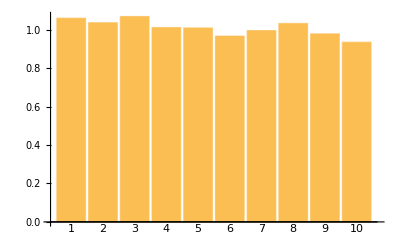

```mathematica
QS1=Table[QS[[i]],{i,1,Length[QS],CHAINS}];
QS1=QS1.MatrixPower[SIGMA,-.5];
QS2=Table[QS[[i]],{i,2,Length[QS],CHAINS}];
QS2=QS2.MatrixPower[SIGMA,-.5];
QS3=Table[QS[[i]],{i,3,Length[QS],CHAINS}];
QS3=QS3.MatrixPower[SIGMA,-.5];
BarChart[StandardDeviation[QS1],ChartLabels->{1,2,3,4,5,6,7,8,9,10}]
```

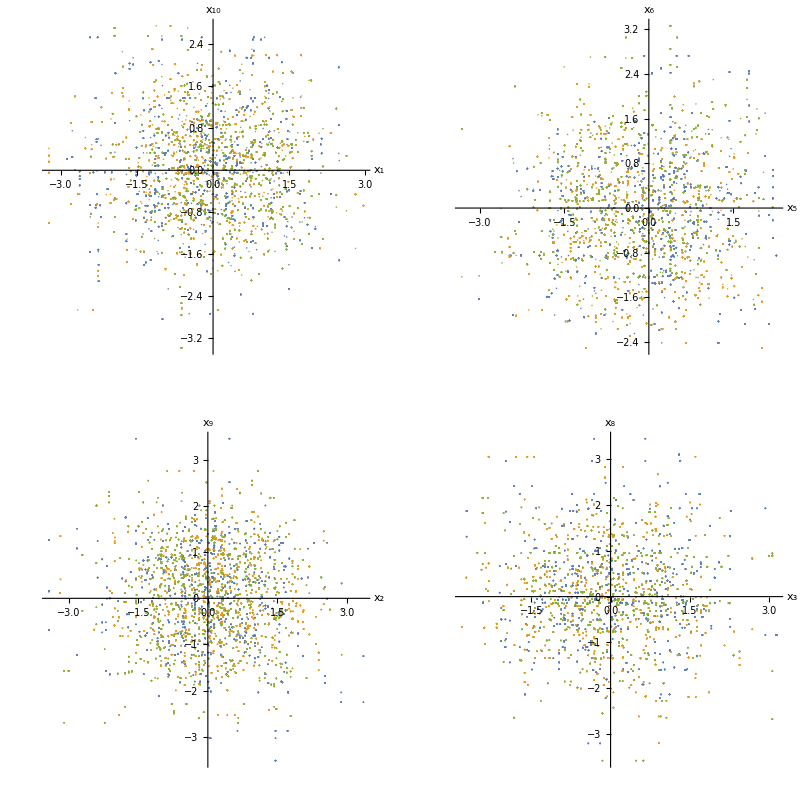

```mathematica
GraphicsGrid[{{ListPlot[{QS1[[;;,{1,10}]],QS2[[;;,{1,10}]],QS3[[;;,{1,10}]]},AspectRatio->1,AxesLabel->{Subscript[x, 1],Subscript[x, 10]}],ListPlot[{QS1[[;;,{5,6}]],QS2[[;;,{5,6}]],QS3[[;;,{5,6}]]},AspectRatio->1,AxesLabel->{Subscript[x, 5],Subscript[x, 6]}]},{ListPlot[{QS1[[;;,{2,9}]],QS2[[;;,{2,9}]],QS3[[;;,{2,9}]]},AspectRatio->1,AxesLabel->{Subscript[x, 2],Subscript[x, 9]}],ListPlot[{QS1[[;;,{3,8}]],QS2[[;;,{3,8}]],QS3[[;;,{3,8}]]},AspectRatio->1,AxesLabel->{Subscript[x, 3],Subscript[x, 8]}]}}]
```

```mathematica
√Diagonal[SIGMA]
```

{1,1/11,1/121,1/1331,1/14641,1/161051,1/1771561,1/19487171,1/214358881,1/2357947691}

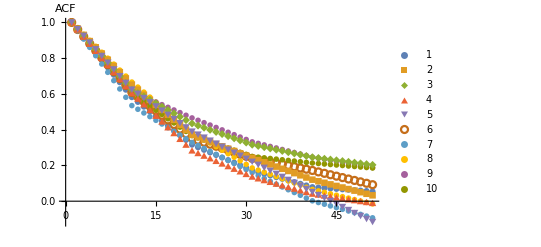

```mathematica
ListPlot[Table[CorrelationFunction[QS1[[Length[QS1]/2;;,i]],{50}],{i,1,10}],PlotRange->All,AxesLabel->{None,"ACF"},PlotLegends->Table[i,{i,1,10}],PlotMarkers->Automatic]
```

```mathematica
psrf[QS]
```

{1.02495,1.00519,1.01227,1.00174,1.00671,1.02623,1.00254,1.00595,1.00044,1.00166}

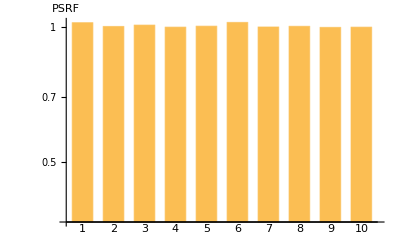

```mathematica
BarChart[psrf[QS]//N,ChartLabels->Table[i,{i,1,10}],BarSpacing->Large,PlotRangeClipping->True,ScalingFunctions->"Log",PlotRange->{Automatic,Automatic},AxesLabel->PSRF]
```